# KdS -- Renormalized angular momentum ν expansion for small η = (rc - rp)/L

This notebook computes expansion for the renormalized angular momentum parameter ν, introduced in the MST formalism for Kerr-de Sitter black holes, in the rotating Nariai limit. The code presented here is based on and accompanies the Bachelor Thesis of Simon Schmitt titled Connecting Monodromies and the Renormalized Angular Momentum in Kerr-de Sitter Spacetimes. The method of obtaining the renormalized angular momentum via the continued fraction equation is based on [1] S. Mano, H. Suzuki, E. Takasugi, Prog. Theor. Phys. 95,  1079, (1996); [2] H. Suzuki, E. Takasugi, and H. Umetsu, Prog. Theor. Phys. 100, 491 (1998); [3] H. Suzuki, E. Takasugi, and H. Umetsu, Prog. Theor. Phys. 102, 253 (1999); [4] H. Suzuki, E. Takasugi, and H. Umetsu, Prog. Theor. Phys. 103, 723 (2000); the QNM expansion is based on [5] F. Novaes, C. I. Marinho, M. Lencs.b4 es, and M. Casals, JHEP 05, 033 (2019), 1811.11912. The exact calculations conducted here are based on the considerations given in the thesis, which is built on initial work by Marc Casals.  More detailed references are given in the thesis.

The ν considered here corresponds to the new \check{ν} from the thesis. The expansions are obtained as ν = ν0 + ν1 η + O(η^2), where η = (r_C - r_+)/L is the extremality parameter. In this code, the coefficients ν0 and ν1 are obtained, but in principle this code should allow to extract arbitrary orders of the expansions. The expansions are done for azimuthal number m=0 and spin-weight s=0; however, this code allows straightforward generalization to arbitrary m and s up to calculational difficulty. The expansions are done at QNM frequencies ω = omegaBar0 η + omegaBar1 η^2 + omegaBar2 η^3 with the coefficients derived in [5]. The reason for this choice is discussed in the thesis.

The code is split in three parts:
1. The first chapter parametrizes the black hole in terms of the horizon r_+ and r_C with L=1, c.f. thesis section 2.1, and sets up the toolkit which is used in expanding quantities, in particular “KdSSeries”.
2. The second chapter builds the continued fraction equation. 
3. The third chapter extracts the coefficients of the expansion from the continued fraction equation. It splits into
	3.a. The coefficients are extracted in terms of the event horizon r_+. 
	3.b. The continued fraction equation is reexpanded in terms of α=a^2/L^2. Coefficients are obtained as a function of α. This is used to verify the QNM condition ν = θ_C - θ_+ mod 1 by expanding both sides.

Chapters 1 and 2 therefore constitute the setup for the continued fraction equation, which is stored in a separate file after it is first calculated. Thus, after running the notebook once, the user can jump straight into chapter 3. It should be noted though that it is required that chapter 1  has been executed for chapter 3, in particular section 10, to work.

```mathematica
Clear["Global`*"];

Print["====================================================================="];
Print["KdS Renormalized angular momentum ν expansion for small η = rc - rp"];
Print["======================================================================"];

(* We set the order in η of our expansions (of every parameter) throughout. Some of the parameters are expanded to higher orders to ensure that there are no truncation errors, which is controlled by maxOrder *)
expansionOrder = 3;
maxOrder       = expansionOrder + 3;

(* We make sure that m=s=0 everywhere where the parameters are potentially introduced. For future generalizations, this can be used to set m and s throughout.*)
s=0; 
m=0; 
(* We set the depth at which the continued fraction is calculated. It is important to set it here in the beginning, since both chapters 2 and 3 depend on it and since it indexes the name of the cached file.*) 
cfDepth = 4;
```

============================================================

KdS Renormalized angular momentum ν expansion for small η = rc - rp

============================================================

## I. Setup

In this chapter the necessary preparation is done to create the continued fraction equation in the following section. Every parameter is first expressed exclusively in terms of the horizons r_+ and r_C (L=1) following thesis section 2.1. These are then expanded in terms of η = (r_C - r_+)/L = r_C - r_+. Finally, auxiliary functions are defined, which conveniently expand any quantity in terms of η up to expansionOrder, with coefficients exclusively parametrized in r_+.

The most challenging part in obtaining the expansion for ν is the fact that the expressions obtained, even at intermediate steps, quickly get bloated. For this reason, this code tries to implement a delicate balance between early and aggressive simplifications, and acceptable runtimes of the notebook. Achieving this balance has been the main challenge throughout this part of the thesis and thus, in the eyes of the author, represents the main contribution of the this code. This is further the reason why throughout the code, byte- and leafcounts are repeatedly displayed; we keep this to facilitate future debugging.

```mathematica
Print[""];
Print["Imposing global assumptions on r_+ and other parameters:"];

$Assumptions = And[rp >= 0, rp <= 1/Sqrt[3], l>=0, α∈Reals, α>=0];
Print["$Assumptions = ", $Assumptions];
```

Imposing global assumptions on r_+ and other parameters:

$Assumptions = rp≥0&&rp≤1/(√3)&&l≥0&&α∈ℝ&&α≥0

```mathematica
(* =====================================================================
   Section 1 - Exact symbolic expressions in terms of r_C and r_+
   ===================================================================== *)

(* This cell obtains symbolic expressions for all necessary quantities in terms of r_+ and r_C, cf. thesis section 2.1*)

Print["[Sec 1] Setting L = 1, solving for a^2 and M..."];

(* Horizon function with L = 1 *)
Deltar[r_, a_, M_] := (r^2 + a^2)(1 - r^2) - 2 M r;

(* The resulting system is linear in M, so that no branch issues arise. For derivations cf. thesis section 2.1*)
LsqSym  = 1;
asqSym  = rp rc (1 - (rp^2 + rp rc + rc^2))/(1 + rp rc);
MSym    = (rp^2 + asqSym)(1 - rp^2)/(2 rp) // Simplify;
alpha2SymNovaes = asqSym/LsqSym // Simplify;     (* = asqSym since L=1 *)

(* Remaining quadratic: r^2 + (rp+rc) r + c0, c0 = -asq/(rp rc) *)
c0Sym   = -asqSym/(rp rc) // Simplify;
discSym = (rp + rc)^2 - 4 c0Sym // Simplify;
rmSym   = (-(rp + rc) + Sqrt[discSym])/2 // Simplify;
rmmSym  = (-(rp + rc) - Sqrt[discSym])/2 // Simplify;

Print["[Sec 1] Done. LeafCounts: asqSym=",   LeafCount[asqSym], ", LsqSym=",   LeafCount[LsqSym], ", alpha2Sym=", LeafCount[alpha2SymNovaes], ", rmSym=",    LeafCount[rmSym]];
```

[Sec 1] Setting L = 1, solving for a^2 and M...

[Sec 1] Done. LeafCounts: asqSym=26, LsqSym=1, alpha2Sym=22, rmSym=41

```mathematica
(* =====================================================================
   Section 2  --  Pre-expand building blocks in η = rc - rp
   ===================================================================== *)
Print[""];
Print["[Sec 2] Pre-expanding building blocks to maxOrder = ", maxOrder, "..."];

(* This section preexpands important, reoccuring quantities once in η up to maxOrder, so that later they only have to inserted and not recalculated. The whole cell takes a moment (<60s) to execute, but this saves signifiant compute time later. *)
asqSeries    = Series[asqSym    /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;
LsqSeries    =  Series[LsqSym    /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;

(*Important: In [2-4], it is α=a^2/L^2, whereas in [5] it is α=a/L. This justifies the following distinction. Throughout this code, whenever we simply write α symbolically, we mean α=a^2/L^2 *)
alpha2SeriesNovaes =  Series[alpha2SymNovaes /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;
alphaSeriesSTU = alpha2SeriesNovaes;
alpha2SeriesSTU = Series[alpha2SeriesNovaes^2, {η, 0, maxOrder}] // FullSimplify;
alphaSeriesNovaes =   Series[Sqrt[alpha2SymNovaes] /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;

aSeries     =   Series[Sqrt[asqSym]    /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;
LSeries     =   Series[Sqrt[LsqSym]    /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;
rmSeries    =   Series[rmSym  /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;
rmmSeries   =   Series[rmmSym /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;
MSeries =   Series[MSym /. rc -> η + rp, {η, 0, maxOrder}] // FullSimplify;

Print["[Sec 2] Building-block ByteCounts:"];
Print["         asqSeries    = ", ByteCount[asqSeries]];
Print["         LsqSeries    = ", ByteCount[LsqSeries]];
Print["         alpha2SeriesNovaes = ", ByteCount[alpha2SeriesNovaes]];
Print["         alphaSeriesNovaes  = ", ByteCount[alphaSeriesNovaes]];
Print["         rmSeries     = ", ByteCount[rmSeries]];
Print["         rmmSeries    = ", ByteCount[rmmSeries]];

(* We equally preexpand inverse factors of important quantities. This has proven to reduce compute time later on significantly *)
invAlphaSeriesNovaes       =  Series[1/alphaSeriesNovaes,            {η, 0, maxOrder}] // FullSimplify;
invAlpha2SeriesNovaes      =  Series[1/alpha2SeriesNovaes,           {η, 0, maxOrder}] // FullSimplify;
invAlphaSeriesSTU = Series[1/alphaSeriesSTU,           {η, 0, maxOrder}] // FullSimplify;
invAlpha2SeriesSTU = Series[1/alphaSeriesSTU^2, {η, 0, maxOrder}] // FullSimplify;
invRpMinusRmSeries   =  Series[1/(rp - rmSeries),        {η, 0, maxOrder}] // FullSimplify;
invRpMinusRmSqSeries =  Series[1/(rp - rmSeries)^2,      {η, 0, maxOrder}] // FullSimplify;
invRpMinusRmmSeries  =  Series[1/(rp - rmmSeries),       {η, 0, maxOrder}] // FullSimplify;
invRmMinusRmmSeries  =  Series[1/(rmSeries - rmmSeries), {η, 0, maxOrder}] // FullSimplify;

Print["[Sec 2] Inverse-power ByteCounts:"];
Print["         invAlpha2Series      = ", ByteCount[invAlpha2SeriesNovaes]];
Print["         invRpMinusRmSqSeries = ", ByteCount[invRpMinusRmSqSeries]];
Print["         invRpMinusRmmSeries  = ", ByteCount[invRpMinusRmmSeries]];
Print["         invRmMinusRmmSeries  = ", ByteCount[invRmMinusRmmSeries]];
```

[Sec 2] Pre-expanding building blocks to maxOrder = 6...

[Sec 2] Building-block ByteCounts:

asqSeries    = 4128

LsqSeries    = 16

alpha2SeriesNovaes = 4128

alphaSeriesNovaes  = 13280

rmSeries     = 8560

rmmSeries    = 8584

[Sec 2] Inverse-power ByteCounts:

invAlpha2Series      = 7568

invRpMinusRmSqSeries = 32216

invRpMinusRmmSeries  = 34224

invRmMinusRmmSeries  = 9488

```mathematica
(* =====================================================================
   Section 3  --  Auxiliary Functions
   ===================================================================== *)
Print[""];
Print["[Sec 3] Loading auxiliary functions..."];

KdSSeriesRules = {
  (* We manually catch inverse powers of important quantities so that it does not depend on whether Mathematica is capable of correctly finding them;
  and also this does not force mathematica to take 1/alphaSeries and recalculate it into a 1/eta free series. *)
  Power[α, -1]   -> invAlphaSeriesSTU,
  Power[α, -2]   -> invAlpha2SeriesSTU,
  Power[rp - rm,  -1]   -> invRpMinusRmSeries,
  Power[rp - rm,  -2]   -> invRpMinusRmSqSeries,
  Power[rp - rmm, -1]   -> invRpMinusRmmSeries,
  Power[rm - rmm, -1]   -> invRmMinusRmmSeries,
  (* We separate asq and Lsq for from a and L to not be dependent on Mathematica correctly distinguishing the powers.  *)
  asq      -> asqSeries,
  Lsq      -> LsqSeries,
  a        -> aSeries,
  L        -> LSeries,
  M -> MSeries,
  α -> alphaSeriesSTU,
  alpha2   -> alpha2SeriesSTU,
  rm       -> rmSeries,
  rmm      -> rmmSeries,
  rc       -> rp + η,
  ω -> omegaBar0 η + omegaBar1 η^2 + omegaBar2 η^3, (* This is the QNM expansion for the frequency as derived in [5]. The reason one has to insert this to obtain truncating expressions in η for the continued fraction equation is discussed in the thesis 6.2 *)
  λs -> λs0 + λs1 η + λs2 η^2 (* We have to assume that λ is expandable in η. At QNMs, this follows from the coefficients obtained in [5] (Appendix E).*)
};

(* This expands a designated quantity up to expansionOrder, expresses everything in terms of rp and eta and unwraps the SeriesData to a Polynomial                   *)
KdSExpand[expr_, order_Integer : expansionOrder] := Normal[Series[expr /. KdSSeriesRules, {η, 0, order}]];

(* Same, but keep the SeriesData wrapper for further series arithmetic. *)
KdSSeries[expr_, order_Integer : expansionOrder] := Series[expr /. KdSSeriesRules, {η, 0, order}];

(* This evaluates any parameter in the rotating Nariai limit                          *)
KdSExtremal[expr_] := reduceQ[expr /. KdSSeriesRules /. η -> 0];

Print["[Sec 3] KdSExpand, KdSSeries, KdSExtremal ready."];

(* Probe: horizon condition.  Deltar(rp) must be 0 at every order in eta. This verifies that the calculations in section 1 and expansions in section 2 have been implemented correctly. *)
Module[{test1},
  test1 = KdSExpand[(rp^2 + asq)(1 - rp^2/Lsq) - 2 M rp, 2] // Together;
  Print["[Sec 3] Horizon test Deltar(rp) (expect 0): ", test1];
  test2 = KdSSeries[(rp^2 + asq)(1 - rp^2/Lsq) - 2 M rp, 2];
  Print["[Sec 3] Horizon test Deltar(rp) (expect O(η^3): ", test2];
];
```

[Sec 3] Loading auxiliary functions...

[Sec 3] KdSExpand, KdSSeries, KdSExtremal ready.

[Sec 3] Horizon test Deltar(rp) (expect 0): 0

[Sec 3] Horizon test Deltar(rp) (expect O(η^3): O[η]^3

## II. Continued Fraction Equation

In this chapter, all the parameters required for the construction of the continued fraction equation are defined. The necessary parameters (Heun paramaters etc.) are defined and expanded corresponding to [2] and the thesis. From the beginning, we implement the swap A_2 <-> A_3 (cf. e.g δ= 2A_3 +1) and v -> ξ_r v. Many simplifications to speed up compute time have been implemented via trial and error.

Note that the continued fraction equation itself is only calculated in the beginning of next chapter. The reason for this is that we store the continued fraction equation separately, such that chapters 1 and 2 have to be executed only once in principle, and afterwards one can jump straight into chapter 3.

```mathematica
(* ======================================================================================
   Section 4  --  Physical building blocks: a_i, A_i+/-, Heun params, ξ_r, vξ_r_i
   ====================================================================================== *)
Print[""];
Print["[Sec 4] Building physical Heun parameters and v_epsilon_r..."];

(* Imaginary parameters defined in [2] *)
a1 = asq I (1 + α)/α ω (rp^2 + asq)/((rc - rp)(rmm - rp)(rm - rp)) // FullSimplify;
a2 = asq I (1 + α)/α ω (rm^2 + asq)/((rc - rm)(rmm - rm)(rp - rm)) // FullSimplify;
a3 = asq I (1 + α)/α ω (rc^2 + asq)/((rm - rc)(rmm - rc)(rp - rc)) // FullSimplify;
a4 = asq I (1 + α)/α ω (rmm^2 + asq)/((rm - rmm)(rc - rmm)(rp - rmm)) // FullSimplify;

a1Series = KdSSeries[a1, expansionOrder] // Simplify;
Print["[Sec 4] a1 expanded.  ByteCount = ", ByteCount[a1Series]];
a2Series = KdSSeries[a2, expansionOrder] // Simplify;
Print["[Sec 4] a2 expanded.  ByteCount = ", ByteCount[a2Series]];
a3Series = KdSSeries[a3, expansionOrder] // Simplify;
Print["[Sec 4] a3 expanded.  ByteCount = ", ByteCount[a3Series]];
a4Series = KdSSeries[a4, expansionOrder] // Simplify;
Print["[Sec 4] a4 expanded.  ByteCount = ", ByteCount[a4Series]];

(* Sign conventions as given in the thesis. We remind the reader that s=0. *)
A1Series  = -a1Series;
A2Series  =  a2Series;
A3Series  =  a3Series;
A4SeriesP =  a4Series;
A4SeriesM = -a4Series;

(* Heun parameters: We directly include the switch A2 <-> A3 into the definition of the Heun-parameters, 
such that oll of the expressions (e.g. β) can be directly expressed in the original Heun parameters. *)
γ   = 2 A1Series + 1;
δ   = 2 A3Series + 1;
ϵ = 2 A2Series + 1;
σp  = A1Series + A2Series + A3Series + A4SeriesM + 1;
σm  = A1Series + A2Series + A3Series + A4SeriesP + 1;
ωH  = γ + δ - 1;

Print["[Sec 4] Heun parameters defined."];


(* v*ξ_r is one of the most compute intensive parts of the coefficients. For this reason, it is split up and simplifications are applied individually to obtain the best results and balance*)

(* ξr is 1/x_r from the thesis*)
ξr = ((rm - rp)(rc - rmm))/((rm - rmm)(rc - rp));
ξr = KdSSeries[ξr, expansionOrder] // Simplify;
Print["[Sec 4] xi_r expanded.  ByteCount = ", ByteCount[ξr]];

(* v_ξ_r_1: An optimized expansion expanding everything early and individually, then trying to exploit the speed of Series Arithmetic. *)
vξr1Series = Module[
  {ord = maxOrder, sA, sP, sI2, sRM, sMM, sRR, sB, raw},
  sA  = KdSSeries[asq^2,                 ord] // Simplify;
  sP  = KdSSeries[(1 + α)^2,       ord] // Simplify;
  sI2 = KdSSeries[1/α^2,           ord] // Simplify;
  sRM = KdSSeries[1/(rp - rm)^2,          ord]// Simplify;
  sMM = KdSSeries[1/(rp - rmm),           ord] // Simplify;
  sRR = KdSSeries[1/(rm - rmm),           ord] // Simplify;
  sB  = KdSSeries[(-ω^2rp^3(rp*rm - 2*rm*rc+rp*rc)+2*asq*ω^2*rp(rm*rc-rp^2)-asq*asq*ω^2(2*rp-rm-rc)), ord] // Simplify;
  Simplify[2 η^(-3) sA sP sI2 sRM sMM sRR sB]
];
Print["[Sec 4] v_epsilon_r_1 expanded.  ByteCount = ", ByteCount[vξr1Series]];

vξr2Series = Simplify[KdSSeries[-(- 2 rmm^2/((rm - rmm)(rc - rp)) + (rc - rmm)/(rc - rp)), expansionOrder]] - ((1 + ξr) A1Series + A2Series + ξr A3Series);
Print["[Sec 4] v_epsilon_r_2 expanded.  ByteCount = ", ByteCount[vξr2Series]];

vξr3Series = -2 A1Series (A2Series + ξr A3Series);
Print["[Sec 4] v_epsilon_r_3 expanded.  ByteCount = ", ByteCount[vξr3Series]];

(* v_ξ_r_4: Similar to above*)
vξr4Series = Module[
  {ord = expansionOrder + 1, sA, sI, sRM, raw},
  sA  = KdSSeries[asq*λs,             ord]// Simplify;
  sI  = KdSSeries[1/α,      ord]// Simplify;
  sRM = KdSSeries[1/(rm - rmm),    ord] // Simplify;
  Simplify[η^(-1) sA sI sRM]
];
Print["[Sec 4] v_epsilon_r_4 expanded.  ByteCount = ", ByteCount[vξr4Series]];
```

[Sec 4] Building physical Heun parameters and v_epsilon_r...

[Sec 4] a1 expanded.  ByteCount = 14816

[Sec 4] a2 expanded.  ByteCount = 15408

[Sec 4] a3 expanded.  ByteCount = 14640

[Sec 4] a4 expanded.  ByteCount = 14840

[Sec 4] Heun parameters defined.

[Sec 4] xi_r expanded.  ByteCount = 8848

[Sec 4] v_epsilon_r_1 expanded.  ByteCount = 81096

[Sec 4] v_epsilon_r_2 expanded.  ByteCount = 89936

[Sec 4] v_epsilon_r_3 expanded.  ByteCount = 107432

[Sec 4] v_epsilon_r_4 expanded.  ByteCount = 10776

```mathematica
(* =====================================================================
   Section 5  --  Three-term recurrence coefficients original + optimized versions)
   ===================================================================== *)
Print[""];
Print["[Sec 5] Defining recurrence coefficients..."];

(* This section obtains expansions of the recurrence coefficients α, β, γ. We give both the original definitions in terms of Heun parameters, as well as the employed simplified ones according to section 5.1 in the thesis for optimization. *)

(* This is the general definition of β (without vξr!), kept for verification. *)
βcoeff[k_] := ((1 - ωH)(γ - δ)(σp - σm + ϵ - 1)(σp - σm - ϵ + 1)) /(32 (k + ν)(k + ν + 1))+ ((1/2) - ξr)(k + ν)(k + ν + 1)+ (1/4)(ϵ (γ - δ)+ δ (1 - ωH)+ 2 σp σm)+ (ωH^2 - 1)/4 ξr;

(* =  We use the sign choices in the thesis to algebraically simplify the first term (cf. thesis section 5.1) to increase performance. *)
βcoeffOpt[k_] := -((a1Series^2 - a3Series^2)(a4Series^2 - a2Series^2))/(2 (k + ν)(k + ν + 1)) + ((1/2) - ξr)(k + ν)(k + ν + 1) + (1/4)(ϵ (γ - δ)+ δ (1 - ωH)+ 2 σp σm)+ (ωH*ωH - 1)/4 *ξr;

(* These are the original definitions for α and γ, kept for verification.  *)
αcoeff[k_] := -(((k + ν) - ωH/2 + 3/2)((k + ν) - σp + ωH/2 + 3/2)((k + ν) - σm + ωH/2 + 3/2)((k + ν) + δ - ωH/2 + 1/2)) /(2 (2 (k + ν) + 3)((k + ν) + 1));

γcoeff[k_] := -(((k + ν) + σp - ωH/2 - 1/2)((k + ν) + σm - ωH/2 - 1/2)((k + ν) + γ - ωH/2 - 1/2)((k + ν) + ωH/2 - 1/2)) /(2 (2 (k + ν) - 1)(k + ν));


(* We define the coefficients as functions who memoize the expressions after they are first called. The current form of these coefficients is due to careful optimization; of course, they are equivalent to the original definitions given above. *)

Clear[βnSeriesWithAnsatz, αnSeriesWithAnsatz, γnSeriesWithAnsatz];

(* β is calculated using the optimized first part, as well as the expression for vξr which is independent of n (this is the reason it was so convenient to once calculate it in the previous section). *)
βnSeriesWithAnsatz[k_] := βnSeriesWithAnsatz[k] =
  KdSSeries[βcoeffOpt[k] /. ν -> ν0 + ν1 η + ν2 η^2, expansionOrder] + vξr1Series + vξr2Series + vξr3Series + vξr4Series;

(* Optimized calculation for α, same for γ:
   Numerator = product of four series (each linear in nu_sub + Heun).
   Denominator = 2 (2 m + 2 nu_sub + 3)(m + nu_sub + 1)
               -- polynomial in nu0, nu1, nu2, m, eta; no radicals.
   The denominator inverse is a fast series; we then multiply.       *)
αnSeriesWithAnsatz[m_] := αnSeriesWithAnsatz[m] = Module[{nuSub, ord, s1, s2, s3, s4, sd1, sd2, num, denInv},
    nuSub = ν0 + ν1 η + ν2 η^2;
    ord   = expansionOrder;
    s1  = KdSSeries[m + nuSub - ωH/2 + 3/2,        ord] // Simplify;
	s2  = KdSSeries[m + nuSub - σp + ωH/2 + 3/2,   ord] // Simplify;
	s3  = KdSSeries[m + nuSub - σm + ωH/2 + 3/2,   ord] // Simplify;
	s4  = KdSSeries[m + nuSub + δ  - ωH/2 + 1/2,   ord]// Simplify;
	sd1 = KdSSeries[2 (2 m + 2 nuSub + 3),          ord] // Simplify;
	sd2 = KdSSeries[m + nuSub + 1,                  ord] // Simplify;
	num = s1 s2 s3 s4; 
	denInv = KdSSeries[1/(sd1 sd2),                 ord] // Simplify;
    -num denInv                                       (* SeriesData -- auto-truncates *)
  ];
  
γnSeriesWithAnsatz[m_] := γnSeriesWithAnsatz[m] = Module[{nuSub, ord, s1, s2, s3, s4, sd1, sd2, num, denInv},
    nuSub = ν0 + ν1 η + ν2 η^2;
    ord   = expansionOrder;
    s1  = KdSSeries[m + nuSub + σp - ωH/2 - 1/2, ord] // Simplify;
    s2  = KdSSeries[m + nuSub + σm - ωH/2 - 1/2, ord] // Simplify;
    s3  = KdSSeries[m + nuSub + γ  - ωH/2 - 1/2, ord] // Simplify;
    s4  = KdSSeries[m + nuSub + ωH/2 - 1/2, ord] // Simplify;
    sd1 = KdSSeries[2 (2 m + 2 nuSub - 1), ord] // Simplify;
    sd2 = KdSSeries[m + nuSub, ord] // Simplify;
    num    = s1 s2 s3 s4;
    denInv = KdSSeries[1/(sd1 sd2), ord] // Simplify;
    -num denInv    
  ];

Print["[Sec 5] All coefficients defined; with-ansatz series will memoise on first call."];
```

[Sec 5] Defining recurrence coefficients...

[Sec 5] All coefficients defined; with-ansatz series will memoise on first call.

```mathematica
(* =====================================================================
   Section 6  --  Pre-caching coefficients
   ===================================================================== *)
Print[""];
Print["[Sec 6] Pre-caching with-ansatz coefficients over k in {", -cfDepth, "...", cfDepth"} ..."];

(* This section simply memoizes the coefficients required to build the continued fraction equation up to the depth set above. The prints are diagnostics which can of course be enabled/disabled to ones liking.*)

Do[
  βnSeriesWithAnsatz[k];
  Print["[Sec 6]   beta[",  k, "] cached, ByteCount = ",
        ByteCount[βnSeriesWithAnsatz[k]]];
  αnSeriesWithAnsatz[k];
  Print["[Sec 6]   alpha[", k, "] cached, ByteCount = ",
        ByteCount[αnSeriesWithAnsatz[k]]];
  γnSeriesWithAnsatz[k];
  Print["[Sec 6]   gamma[", k, "] cached, ByteCount = ",
        ByteCount[γnSeriesWithAnsatz[k]]];
, {k, -cfDepth, cfDepth}];

Print["[Sec 6] Done."]
```

[Sec 6] Pre-caching with-ansatz coefficients over k in {-4...4 } ...

[Sec 6]   beta[-4] cached, ByteCount = 504208

[Sec 6]   alpha[-4] cached, ByteCount = 150304

[Sec 6]   gamma[-4] cached, ByteCount = 150304

[Sec 6]   beta[-3] cached, ByteCount = 504208

[Sec 6]   alpha[-3] cached, ByteCount = 150304

[Sec 6]   gamma[-3] cached, ByteCount = 150304

[Sec 6]   beta[-2] cached, ByteCount = 504208

[Sec 6]   alpha[-2] cached, ByteCount = 150304

[Sec 6]   gamma[-2] cached, ByteCount = 150304

[Sec 6]   beta[-1] cached, ByteCount = 503920

[Sec 6]   alpha[-1] cached, ByteCount = 146656

[Sec 6]   gamma[-1] cached, ByteCount = 150304

[Sec 6]   beta[0] cached, ByteCount = 503728

[Sec 6]   alpha[0] cached, ByteCount = 150376

[Sec 6]   gamma[0] cached, ByteCount = 146264

[Sec 6]   beta[1] cached, ByteCount = 504208

[Sec 6]   alpha[1] cached, ByteCount = 150376

[Sec 6]   gamma[1] cached, ByteCount = 150376

[Sec 6]   beta[2] cached, ByteCount = 504208

[Sec 6]   alpha[2] cached, ByteCount = 150376

[Sec 6]   gamma[2] cached, ByteCount = 150376

[Sec 6]   beta[3] cached, ByteCount = 504208

[Sec 6]   alpha[3] cached, ByteCount = 150376

[Sec 6]   gamma[3] cached, ByteCount = 150376

[Sec 6]   beta[4] cached, ByteCount = 504208

[Sec 6]   alpha[4] cached, ByteCount = 150376

[Sec 6]   gamma[4] cached, ByteCount = 150376

[Sec 6] Done.

## III. ν - Expansions

In  this chapter, the coefficients in the expansion ν = ν0 + ν1 η + O(η^2) are extracted from the continued fraction equation. This is done by organizing the continued fraction equation in powers of η, and requiring the coefficient of each power to vanish independently. 

Two different types of coefficients are obtained: 
- In IIIa, we simply extract the coefficients via the outlined procedure, which are then a function of r_+. In these expressions, λs_i is left symbolic since no expressions for them are known in terms of r_+. 
- In IIIb, we want to insert the coefficients given in [5] for the λ-expansion. These are given as additional expansions in α. For this reason, in IIIb, we reexpress the entire continued fraction equation in terms of α and thus extract coefficients which are functions of α. These can then be compared to the coefficients in the expansions of the RHS of the QNM condition, i.e. of θ_C - θ_+. 

After a first calculation, the continued fraction equation is stored in a separate file. Thus, when first running the notebook, one needs to first execute chapters 1 and 2. After the separate file is obtained, this chapter works completely independently of the previous ones.

## III.a. Extraction of coefficients as functions of r_+

```mathematica
(* =====================================================================
   Section 7  --  Continued fractions + recurrence assembly
   ===================================================================== *)
Clear[recurrence];
Clear[cfαnRnp1, cfγnLnm1];


(* This is the implementation of the continued fractions R_n and L_n from [2]/ the thesis. Note that the first is alreadly α_n * R_{n+1}, and the second is γ_n * L_{n-1}. *)
cfαnRnp1[n_, nMax_] := cfαnRnp1[n, nMax] = If[n >= nMax, 0, -αnSeriesWithAnsatz[n] * γnSeriesWithAnsatz[n + 1] /(βnSeriesWithAnsatz[n + 1] + cfαnRnp1[n + 1, nMax])];

cfγnLnm1[n_, nMin_] := cfγnLnm1[n, nMin] = If[n <= nMin, 0, -γnSeriesWithAnsatz[n] * αnSeriesWithAnsatz[n - 1] / (βnSeriesWithAnsatz[n - 1] + cfγnLnm1[n - 1, nMin])];

Print["[Sec 6] Continued fractions defined.  Assembling recurrence..."];

cacheFile = FileNameJoin[{NotebookDirectory[], StringJoin["continuedFractionDepth", ToString[cfDepth], ".mx"]}];

If[FileExistsQ[cacheFile],
  (* If the file already exists, the continued fraction equation is loaded from there.*)
  Get[cacheFile];
  Print["[Sec 6] Loaded cached recurrence from disk."],

  (* If the continued fraction equation is not found, it is calculated recursively and then stored to the new file.*)
  Print["[Sec 6] No cache found. Assembling recurrence..."];
  recurrence = βnSeriesWithAnsatz[0] + cfαnRnp1[0, cfDepth] + cfγnLnm1[0, -cfDepth];
  DumpSave[cacheFile, recurrence];
  Print["[Sec 6] Computed and cached recurrence to ", cacheFile];
];

(* These are diagnostics run whether loaded or freshly computed. They in particular tell us if the coefficients of the expansions have found their way into the continued fraction equation. *)
Print["[Sec 6]   Head:      ", Head[recurrence]];
Print["[Sec 6]   ByteCount: ", ByteCount[recurrence]];
Print["[Sec 6]   LeafCount: ", LeafCount[recurrence]];
Print["[Sec 6]   Contains nu0/nu1/nu2: ",
      ! FreeQ[recurrence, #] & /@ {ν0, ν1, ν2}];
```

[Sec 6] Continued fractions defined.  Assembling recurrence...

[Sec 6] Loaded cached recurrence from disk.

[Sec 6]   Head:      SeriesData

[Sec 6]   ByteCount: 752240

[Sec 6]   LeafCount: 24767

[Sec 6]   Contains nu0/nu1/nu2: {True,True,True}

```mathematica
(* =====================================================================
   Section 8  --  Organizing the continued fraction Equation
   ===================================================================== *)
 
(* This short auxiliary section extracts the list of coefficients (of powers of η) from the continued fraction equation and associated parameters. Additionally, it offers a diagnostic to see if the ν coefficients cascade nicely. *)

coeffList = recurrence[[3]];
ordMin    = recurrence[[4]];
ordMax   = recurrence[[5]];
den     = recurrence[[6]];

Print["[Sec 7]   Laurent range: eta^", ordMin/den,
      " ... eta^", (ordMax - 1)/den,
      "   (#stored coeffs = ", Length[coeffList], ")"];

(* The following is a very useful diagnostic tool. It is supposed to be read as follows: For each power of η in the continued fraction equation, we look at the corresponding coefficients. We then display their byte counts, and more importantly, whether they 
contain the coeffcients of the QNM expansions (omegaBar) and the coeffcients of the ν expansions, where the "Y" indicates it contains the respective coefficient, and a dot indicates its absence. 
Important: Many of the omegaBar dependencies display here turn out to be artificial, since they vanish after simplification. This is expected, since e.g. the omegaBar0 contribution stems from a factor of ω^2 at a power of η^-1, which should therefore via the QNM
expansion be promoted to a power of η^1. *)
Print["[Sec 7]   Per-eta-order symbol map:"];
Do[
  With[{exp = ordMin/den + (idx - 1)/den,
        c = coeffList[[idx]]},
    Print["          eta^", PaddedForm[exp, 2],
          "  bytes=", PaddedForm[ByteCount[c], 8],
          "  | oB0=", If[!FreeQ[c, omegaBar0], "Y", "."],
          "  oB1=", If[!FreeQ[c, omegaBar1], "Y", "."],
          "  oB2=", If[!FreeQ[c, omegaBar2], "Y", "."],
          "  nu0=", If[!FreeQ[c, ν0], "Y", "."],
          "  nu1=", If[!FreeQ[c, ν1], "Y", "."],
          "  nu2=", If[!FreeQ[c, ν2], "Y", "."]
        ];
  ];
, {idx, Length[coeffList]}];
```

[Sec 7]   Laurent range: eta^-1 ... eta^2   (#stored coeffs = 4)

[Sec 7]   Per-eta-order symbol map:

eta^ -1  bytes=    10032  | oB0=Y  oB1=.  oB2=.  nu0=Y  nu1=.  nu2=.

eta^  0  bytes=    52592  | oB0=Y  oB1=Y  oB2=.  nu0=Y  nu1=Y  nu2=.

eta^  1  bytes=   171352  | oB0=Y  oB1=Y  oB2=Y  nu0=Y  nu1=Y  nu2=Y

eta^  2  bytes=   518040  | oB0=Y  oB1=Y  oB2=Y  nu0=Y  nu1=Y  nu2=Y

```mathematica
(* =====================================================================
   Section 8 - Extraction of coefficients
   ===================================================================== *)
(* In this section, the coefficients as functions of r_+ are finally extracted. *)

coeffm1 = coeffList[[1]] // Simplify;
nu0Sol = Solve[coeffm1 == 0, ν0] // FullSimplify;
nu01 = Values[nu0Sol[[1]]][[1]];
nu02 = Values[nu0Sol[[2]]][[1]];

coeff0 = coeffList[[2]]/. nu0Sol // Simplify;

nu11=Values[Solve[coeff0[[1]]==0,ν1]][[1]][[1]] // FullSimplify;
nu12=Values[Solve[coeff0[[2]]==0,ν1]][[1]][[1]]//FullSimplify;

(*These are for future purposes if one planes to insert ν1 into the next order to obtain ν2.*)

nu11Replacement = Solve[coeff0[[1]]==0,ν1] // Simplify;
nu12Replacement = Solve[coeff0[[2]]==0,ν1] // Simplify;

Print["The coefficients of the expansion are given by: "];

Print["ν0^{(1)} = ", nu01];
Print["ν0^{(2)} = ", nu02];
Print["ν1^{(1)} = ", nu11];
Print["ν1^{(2)} = ", nu12];
```

The coefficients of the expansion are given by:

ν0^{(1)} = -1/2-(√(-((-1+6 rp^2+3 rp^4) (1+5 rp^4+4 λs0+rp^2 (2+4 λs0)))))/(-2+6 rp^2 (2+rp^2))

ν0^{(2)} = 1/2 (-1+(√(-((-1+6 rp^2+3 rp^4) (1+5 rp^4+4 λs0+rp^2 (2+4 λs0)))))/(-1+6 rp^2+3 rp^4))

ν1^{(1)} = (-λs1+rp (-2-7 λs0+rp (5 λs1+rp (-4-6 λs0+3 rp (3 λs1+rp (2-λs0+rp λs1))))))/((-1+6 rp^2+3 rp^4) √(-((-1+6 rp^2+3 rp^4) (1+5 rp^4+4 λs0+rp^2 (2+4 λs0)))))

ν1^{(2)} = (λs1+rp (2+7 λs0+rp (-5 λs1+rp (4+6 λs0+3 rp (rp (-2+λs0)-(3+rp^2) λs1)))))/((-1+6 rp^2+3 rp^4) √(-((-1+6 rp^2+3 rp^4) (1+5 rp^4+4 λs0+rp^2 (2+4 λs0)))))

## III.b. Extraction of coefficients as functions of α and verification of the QNM condition

```mathematica
(* =====================================================================
   Section 8 - Reexpressing the continued fraction equation in α
   ===================================================================== *)
   
(*In this section, we use the expressions for r_+(α, η) to reexpress the continued fraction equation in terms of an expansion in both η and α. Then we do the same diagnostics as in the r_+ case. This cell takes is expected to take ca. 2 minutes, since the 
reexpansion is compute intensive. However it was the most convenient way to implement the continued fraction equation in terms of α. *)


(* These expressions are from [5] with L=1*)
rcHelper = η/2+1/(2Sqrt[3]) Sqrt[2Sqrt[(α+η^2-1)^2-12α]-2α+η^2+2];
rpHelper = rcHelper-η;

(* We first expand both in η, then reexpand the coefficients in α to obtain the desired double expansion. In principle, we only need to expand everything up to O(α) since we are limited by the expresions for the λ-expansions given in [5] which are equally
only given up to O(α)*)
rpHelperinEta = Series[rpHelper, {η, 0, 3}];
rpHelperinEtaAlpha = Series[rpHelperinEta, {α, 0, 2}];

(* We simply substitute the expressions obtained for r_+ to obtain the continued fraction equation as a double expansion in α and η. The expression is stored in a file, such that it does not have to be recalculated every time. *)
Clear[newRecurrence];

newcacheFile = FileNameJoin[{NotebookDirectory[], StringJoin["AlphaContinuedFractionDepth", ToString[cfDepth], ".mx"]}];

If[FileExistsQ[newcacheFile],
  (* If the file already exists, the continued fraction equation is loaded from there.*)
  Get[newcacheFile];
  Print["[Sec 8] Loaded cached α-recurrence from disk."],

  (* If the continued fraction equation is not found, it is calculated by substitution and then stored to the new file. This step takes ca. 2 minutes.*)
  Print["[Sec 8] No cache found. Assembling α-recurrence..."];
  (*newRecurrence = Series[Normal[recurrence] /. rp -> Normal[rpHelperinEtaAlpha], {η, 0, expansionOrder}];*)
  newRecurrence = Normal[recurrence] /. rp -> rpHelperinEtaAlpha;
  DumpSave[newcacheFile, newRecurrence];
  Print["[Sec 8] Computed and cached α-recurrence to ", newcacheFile];
];


Print["[Sec 8] Recurrence in α assembled."];
Print["[Sec 8]   ByteCount: ", ByteCount[newRecurrence]];
Print["[Sec 8]   LeafCount: ", LeafCount[newRecurrence]];

(*We collect exactly the same information and run the same diagnostic as in the previous section for the r_+ case.*)
newcoeffList = newRecurrence[[3]];
newordMin   = newRecurrence[[4]];
newordMax    = newRecurrence[[5]];
newden     = newRecurrence[[6]];

Print["[Sec 8]   Post-omega Laurent range: eta^", newordMin/newden,
      " ... eta^", (newordMax - 1)/newden,
      "   (#stored coeffs = ", Length[newcoeffList], ")"];

(* Per-eta-order symbol map for cascade planning *)
Print["[Sec 8]   Per-eta-order symbol map:"];
Do[
  With[{exp = newordMin/newden + (idx - 1)/newden,
        c = newcoeffList[[idx]]},
    Print["          eta^", PaddedForm[exp, 2],
          "  bytes=", PaddedForm[ByteCount[c], 8],
          "  | oB0=", If[!FreeQ[c, omegaBar0], "Y", "."],
          "  oB1=", If[!FreeQ[c, omegaBar1], "Y", "."],
          "  oB2=", If[!FreeQ[c, omegaBar2], "Y", "."],
          "  nu0=", If[!FreeQ[c, ν0], "Y", "."],
          "  nu1=", If[!FreeQ[c, ν1], "Y", "."],
          "  nu2=", If[!FreeQ[c, ν2], "Y", "."]
        ];
  ];
, {idx, Length[newcoeffList]}];
```

[Sec 8] Loaded cached α-recurrence from disk.

[Sec 8] Recurrence in α assembled.

[Sec 8]   ByteCount: 8405848

[Sec 8]   LeafCount: 293233

[Sec 8]   Post-omega Laurent range: eta^-1 ... eta^2   (#stored coeffs = 4)

[Sec 8]   Per-eta-order symbol map:

eta^ -1  bytes=    19944  | oB0=Y  oB1=.  oB2=.  nu0=Y  nu1=.  nu2=.

eta^  0  bytes=   176992  | oB0=Y  oB1=Y  oB2=.  nu0=Y  nu1=Y  nu2=.

eta^  1  bytes=  1264352  | oB0=Y  oB1=Y  oB2=Y  nu0=Y  nu1=Y  nu2=Y

eta^  2  bytes=  6944336  | oB0=Y  oB1=Y  oB2=Y  nu0=Y  nu1=Y  nu2=Y

```mathematica
(* =====================================================================
   Section 9 - Extracting coefficients in α
   ===================================================================== *)
 
(* In this section we extract the coefficients of the ν-expansion exactly analogously to the r_+ case. The extraction of ν2 takes is rather compute intensive, so it can be commented out, if this coefficient is not needed.*)

newcoeffm1 = Normal[newcoeffList[[1]]] // Simplify;
newnu0Sol = FullSimplify[Solve[newcoeffm1 == 0, ν0], Assumptions->{ α >= 0}];

nu0α1 = Series[Values[newnu0Sol][[1]], {α, 0, 1}] // FullSimplify;
nu0α2 = Series[Values[newnu0Sol][[2]], {α, 0, 1}] // FullSimplify;

newcoeff0 = newcoeffList[[2]]/. newnu0Sol // FullSimplify;

newnu11Replacement = Solve[Normal[newcoeff0[[1]]]==0,ν1] // Simplify;
newnu12Replacement = Solve[Normal[newcoeff0[[2]]]==0,ν1] // Simplify;

newnu11=Values[Solve[Normal[newcoeff0[[1]]]==0,ν1]][[1]][[1]] // Simplify;
newnu12=Values[Solve[Normal[newcoeff0[[2]]]==0,ν1]][[1]][[1]] // Simplify;

(* We equally extract ν2. This step takes quite a while, since we need to simplify after every step to avoid expression bloat. Thus, one can comment it out in case the coefficient is not needed.
We further note that in principle, since there are two solutions for ν0 and two solutions for ν1, one would need to consider four different coefficients determining ν2. However, it turns out that out of the four solutions
for ν2 obtained, there are two pairs of identical solutions. We have explicitly verified this. This is what one would intuitively expect, and the exact structure with the two remaining solutions being additive inverses of each
other corresponds to the symmetry ν->-ν-1, which is the only known symmetry apart from addition of integers. For these reasons, we only consider two coefficients and obtain two solutions.*)

auxcoeff = newcoeffList[[3]] /. newnu0Sol // Simplify;
auxcoeff2 = auxcoeff /. newnu11Replacement // Simplify;

newcoeff11 = Normal[auxcoeff2][[1]][[1]];
newcoeff12 = Normal[auxcoeff2][[1]][[2]];

newnu21 = Values[Solve[newcoeff11==0,ν2]][[1]][[1]] // Simplify;
newnu22 = Values[Solve[newcoeff12==0,ν2]][[1]][[1]] // Simplify;
```

```mathematica
(* =============================================================================================
   Section 10  - Auxiliary quantities to insert into ν-coefficients, and to verify QNM condition
   ============================================================================================= *)
(* In this section, we establish the necessary quantities like omegaBar_i, λs_i etc., which allow us to obtain explicit expressions for the α-dependent ν-coefficients, and in particular to verify the QNM condition.
All the definitions used here are given in [5]. Not all parameters are used anymore in the following, but we keep them for future ease of use.*)

Print[""];
Print["[Sec 10] Defining necessary parameters..."];

DeltarPrime = Derivative[1, 0, 0][Deltar]; 
Tempp = (Abs[DeltarPrime[rp, aSeries, MSeries]])/(4*Pi*(1+alpha2SeriesNovaes)*(rp^2+asqSeries));
Tempc = (Abs[DeltarPrime[rc, aSeries, MSeries]])/(4*Pi*(1+alpha2SeriesNovaes)*(rc^2+asqSeries));
Ωc = aSeries/(rc^2+asqSeries);
Ωp = aSeries/(rp^2+asqSeries);
Print["[Sec 10] Partly Symbolic helpers defined"];

TpSeries = KdSSeries[Tempp, expansionOrder];
TcSeries = KdSSeries[Tempc, expansionOrder];
ΩcSeries = KdSSeries[Ωc, expansionOrder];
ΩpSeries = KdSSeries[Ωp, expansionOrder];
Print["[Sec 10] Helpers expanded"];

DRprcSeries = KdSSeries[DeltarPrime[rc, aSeries, MSeries], expansionOrder+3];
DRprpSeries = KdSSeries[DeltarPrime[rp, aSeries, MSeries], expansionOrder+3];
DRprmSeries = KdSSeries[DeltarPrime[rm, aSeries, MSeries], expansionOrder+3];
Print["[Sec 10] DeltarPrime expanded"];

θc = I * (1+alpha2SeriesNovaes)(ω (rc^2+asqSeries)/DRprcSeries);
θp = I * (1+alpha2SeriesNovaes) (ω (rp^2+asqSeries)/DRprpSeries);
θm= I * (1+alpha2SeriesNovaes) (ω (rm^2+asqSeries)/DRprmSeries);
Print["[Sec 10] Thetas partially symbolically defined."];

θcSeries = KdSSeries[θc, expansionOrder+3];
θpSeries = KdSSeries[θp, expansionOrder+3];
θmSeries = KdSSeries[θm, expansionOrder+3];
Print["[Sec 10] Thetas expanded."];

RHS = θcSeries- θpSeries // FullSimplify;

newa = Sqrt[α];
newrpBar = (KdSSeries[rp, expansionOrder] /.rp ->rpHelperinEtaAlpha)[[3]][[1]] // Simplify;
newrmBar = (KdSSeries[rm, expansionOrder] /.rp ->rpHelperinEtaAlpha)[[3]][[1]] // Simplify;
newκBar = (newrpBar - newrmBar)(3newrpBar+newrmBar)/((1+α)(newa^2+newrpBar^2)) // Simplify;
newΩBar = (2newa newrpBar)/(newκBar (newa^2+newrpBar^2)^2) // Simplify;
newλsBar = 1/((3newrpBar+newrmBar)(newrpBar-newrmBar))(λs0+2newrpBar^2) // Simplify;
newωBar0InsertionP = Normal[newκBar/2 (-I(omegaOrder + 1/2)+Sqrt[newλsBar-1/4])] // Simplify; (*Note that omegaOrder is the N in [5]; we have chosen this variable name for visibility.*)
newωBar1InsertionP = Normal[(newκBar ((newrpBar-newrmBar)(newrmBar+3newrpBar))^(-1))/(4(2*newωBar0InsertionP/newκBar+I(omegaOrder+1/2)))(λs1)] // FullSimplify;

zeta=Sqrt[12 delta-8 s^2+5];
delta = l(l+1);
newωBar2InsertionP=9/8 Sqrt[3] a (8 a^2-5) m+1/32 I (465 a^2-19) (2 omegaOrder+1)-(3 I (2 omegaOrder+1) (-24 (63 a^2+2) delta^2+8 (21 a^2 (69 m^2-25)-4) delta+3 a^2 (5216 m^2-695)+51))/(32 (4 delta-3) (12 delta+17)^2)+(27 (2 omegaOrder+1)^2)/(16 Sqrt[3] zeta^3 (4 delta-3) (12 delta+17)^2)*(720 (75 a^2-4) delta^4+12 (3 a^2 (300 m^2+3767)-596) delta^3+2 (3 a^2 (1818 m^2+7267)-1054) delta^2+(4439-3 a^2 (7122 m^2+26665)) delta-a^2 (22228 m^2+31937)+1785)+(-10368 (765 a^2-76) delta^5+432 (3 a^2 (8760 m^2-18341)+5236) delta^4+108 (3 a^2 (91484 m^2-49331)+12268) delta^3+6 (9 a^2 (212862 m^2+163295)-166930) delta^2+(-3 a^2 (5249298 m^2-3509465)-951175) delta-15 (a^2 (459664 m^2-155035)+12325))/(16 Sqrt[3] zeta^3 (4 delta-3) (12 delta+17)^2);
cleanωBar2 = newωBar2InsertionP /. {a -> newa, m-> 0} // FullSimplify;


del = delta;
λOmega0 = del+alpha2SeriesNovaes/(del(4del-3))(del(del(2del+1)-2));
λOmega1 = 0;
λOmega2 = 2/(del^3(4del-3))(del^3(del-1));
λOmega3 = 0;

λinOmega = λOmega0 + λOmega1 a ω + λOmega2 asq ω^2 + λOmega3 a^3 ω^3;

λinEta = KdSSeries[λinOmega, expansionOrder+3];

cleanωBar0 = Normal[newωBar0InsertionP] // Simplify;
cleanωBar1 = Normal[newωBar1InsertionP] // Simplify;
cleanωBar2 = newωBar2InsertionP /. {a -> newa, m-> 0} // FullSimplify;

newλ = Normal[λinEta]/. rp -> rpHelperinEtaAlpha;
newλQNM = newλ/.  {omegaBar0 -> cleanωBar0, omegaBar1 -> cleanωBar1, omegaBar2 -> cleanωBar2} // Simplify;

newλQNMmod = newλQNM /. {λs0 -> newλQNM[[3]][[1]], λs1 -> newλQNM[[3]][[2]]} // Simplify;
newλmod2QNM = newλQNMmod /. omegaOrder -> 0; (* This is the choice which makes the later comparison work. A principled reason for this is still unclear.*)

λs0Ins = newλ[[3]][[1]] // FullSimplify;
λs1Ins = newλ[[3]][[2]] // FullSimplify;
λs2Ins = newλ[[3]][[3]] // FullSimplify;

λs0InsQNM = newλmod2QNM[[3]][[1]] // FullSimplify;
λs1InsQNM = newλmod2QNM[[3]][[2]] // FullSimplify;
λs2InsQNM = newλmod2QNM[[3]][[3]] // FullSimplify;

cleanωBar0ForQNMInsertion = cleanωBar0 /. {omegaOrder -> 0, λs0 -> λs0InsQNM}; (* Equally, facilitate later insertion*)

Print["[Sec 10] All quantities established."];
```

[Sec 10] Defining necessary parameters...

[Sec 10] Partly Symbolic helpers defined

[Sec 10] Helpers expanded

[Sec 10] DeltarPrime expanded

[Sec 10] Thetas partially symbolically defined.

[Sec 10] Thetas expanded.

[Sec 10] All quantities established.

```mathematica
(* ==================================================
   Section 11  - Final expressions for ν-coefficients
   ==================================================*)
   
(* We finally obtain the full expressions for the ν-coefficients as a series in α by inserting the λ-coefficients (general) from Section 10 into the coefficients from Section 9 *)

newnu0SolIns = newnu0Sol /. λs0 -> λs0Ins //FullSimplify;

finalnu01 = Series[Values[newnu0SolIns[[1]]][[1]], {α, 0, 1}] // FullSimplify;
finalnu02 = Series[Values[newnu0SolIns[[2]]][[1]], {α, 0, 1}] // FullSimplify;

finalnu11 = Series[newnu11 /. {λs0 -> λs0Ins, λs1 -> λs1Ins}, {α, 0, 1}] // Simplify; 
finalnu12 = Series[newnu12 /. {λs0 -> λs0Ins, λs1 -> λs1Ins}, {α, 0, 1}] // Simplify;

finalnu21 = Series[newnu21 /. {λs0 -> λs0Ins, λs1 -> λs1Ins, λs2 -> λs2Ins}, {α, 0, 1}] // FullSimplify; 
finalnu22 = Series[newnu22 /. {λs0 -> λs0Ins, λs1 -> λs1Ins, λs2 -> λs2Ins}, {α, 0, 1}] // FullSimplify;

Print["The coefficients of the expansion are given by: "];

Print["ν0^{(1)} = ", finalnu01];
Print["ν0^{(2)} = ", finalnu02];
Print["ν1^{(1)} = ", finalnu11];
Print["ν1^{(2)} = ", finalnu12];
Print["ν2^{(1)} = ", finalnu21];
Print["ν2^{(2)} = ", finalnu22];
```

The coefficients of the expansion are given by:

ν0^{(1)} = 1/6 (-3+ⅈ √(15+36 l (1+l)))+(2 ⅈ √3 (-4+3 l (1+l) (-2+5 l (1+l))) α)/((-3+4 l (1+l)) √(5+12 l (1+l)))+O[α]^2

ν0^{(2)} = (-1/2-1/6 ⅈ √(15+36 l (1+l)))-(2 ⅈ √3 (-4+3 l (1+l) (-2+5 l (1+l))) α)/((-3+4 l (1+l)) √(5+12 l (1+l)))+O[α]^2

ν1^{(1)} = O[α]^2

ν1^{(2)} = O[α]^2

ν2^{(1)} = (ⅈ (4 (5+7 omegaBar0^2)+l (1+l) (78+45 l (1+l)+20 omegaBar0^2)))/(2 (17+12 l (1+l)) √(15+36 l (1+l)))-(((191 ⅈ √3-168 √(5+12 l (1+l))+24 l (1+l) (31 ⅈ √3-6 ⅈ √3 l (1+l)+12 √(5+12 l (1+l)))) (-124020-680638 l-1451971 l^2-603066 l^3+3721359 l^4+10104048 l^5+13931352 l^6+12592368 l^7+7570692 l^8+2948400 l^9+589680 l^10+8 (-2774+3 l (1+l) (-2204+3 l (1+l) (37+90 l (1+l) (9+4 l (1+l))))) omegaBar0^2)) α)/(2 ((-3+4 l (1+l)) (5+12 l (1+l))^(3/2) (17+12 l (1+l))^2 (-7 √3+12 √3 l (1+l)+12 ⅈ √(5+12 l (1+l)))^2))+O[α]^2

ν2^{(2)} = -(ⅈ (4 (5+7 omegaBar0^2)+l (1+l) (78+45 l (1+l)+20 omegaBar0^2)))/(2 (17+12 l (1+l)) √(15+36 l (1+l)))-(ⅈ (-124020-680638 l-1451971 l^2-603066 l^3+3721359 l^4+10104048 l^5+13931352 l^6+12592368 l^7+7570692 l^8+2948400 l^9+589680 l^10+8 (-2774+3 l (1+l) (-2204+3 l (1+l) (37+90 l (1+l) (9+4 l (1+l))))) omegaBar0^2) α)/(2 √3 (-3+4 l (1+l)) (5+12 l (1+l))^(3/2) (17+12 l (1+l))^2)+O[α]^2

```mathematica
(* ==========================================================
   Section 11  - Final expressions for ν-coefficients at QNMs
   ==========================================================*)
   
(* We equally obtain the coefficients at QNMs by inserting the QNM coefficients of λ into our ν-coefficients. These will be used for verification of the QNM condition in the next section. *)

newnu0SolInsQNM = newnu0Sol /. λs0 -> λs0InsQNM //FullSimplify;

finalnu01QNM = Series[Values[newnu0SolInsQNM[[1]]][[1]], {α, 0, 1}] // FullSimplify;
finalnu02QNM = Series[Values[newnu0SolInsQNM[[2]]][[1]], {α, 0, 1}] // FullSimplify;

finalnu11QNM = Series[newnu11 /. {λs0 -> λs0InsQNM, λs1 -> λs1InsQNM}, {α, 0, 1}] // Simplify; 
finalnu12QNM = Series[newnu12 /. {λs0 -> λs0InsQNM, λs1 -> λs1InsQNM}, {α, 0, 1}] // Simplify;

finalnu21QNM = FullSimplify[Series[newnu21 /. {λs0 -> λs0InsQNM, λs1 -> λs1InsQNM, λs2 -> λs2InsQNM, omegaBar0 -> cleanωBar0ForQNMInsertion}, {α, 0, 1}], Assumptions->{l>=0}]; 
finalnu22QNM = FullSimplify[Series[newnu22 /. {λs0 -> λs0InsQNM, λs1 -> λs1InsQNM, λs2 -> λs2InsQNM, omegaBar0 -> cleanωBar0ForQNMInsertion}, {α, 0, 1}], Assumptions->{l>=0}];  

Print["The coefficients of the expansion at QNMS are given by: "];

Print["ν0^{(1)} = ", finalnu01QNM];
Print["ν0^{(2)} = ", finalnu02QNM];
Print["ν1^{(1)} = ", finalnu11QNM];
Print["ν1^{(2)} = ", finalnu12QNM];
Print["ν2^{(1)} = ", finalnu21QNM];
Print["ν2^{(2)} = ", finalnu22QNM];
```

The coefficients of the expansion at QNMS are given by:

ν0^{(1)} = 1/6 (-3+ⅈ √(15+36 l (1+l)))+(2 ⅈ √3 (-4+3 l (1+l) (-2+5 l (1+l))) α)/((-3+4 l (1+l)) √(5+12 l (1+l)))+O[α]^2

ν0^{(2)} = (-1/2-1/6 ⅈ √(15+36 l (1+l)))-(2 ⅈ √3 (-4+3 l (1+l) (-2+5 l (1+l))) α)/((-3+4 l (1+l)) √(5+12 l (1+l)))+O[α]^2

ν1^{(1)} = O[α]^2

ν1^{(2)} = O[α]^2

ν2^{(1)} = (61 ⅈ √3+63 √(5+12 l (1+l))+9 l (1+l) (33 ⅈ √3+20 ⅈ √3 l (1+l)+5 √(5+12 l (1+l))))/(12 √(5+12 l (1+l)) (17+12 l (1+l)))-((-31143 ⅈ √3+120879 √(5+12 l (1+l))+l (1+l) (-565223 ⅈ √3+330855 √(5+12 l (1+l))+3 l (1+l) (-493202 ⅈ √3-181665 √(5+12 l (1+l))+18 l (1+l) (13907 ⅈ √3-19086 √(5+12 l (1+l))+80 l (1+l) (755 ⅈ √3-111 ⅈ √3 l (1+l)+246 √(5+12 l (1+l))))))) α)/(2 ((-3+4 l (1+l)) (5+12 l (1+l))^(3/2) (-7 √3+12 √3 l (1+l)+12 ⅈ √(5+12 l (1+l)))^2))+O[α]^2

ν2^{(2)} = (-61 ⅈ √3-63 √(5+12 l (1+l))-9 ⅈ l (1+l) (33 √3+20 √3 l (1+l)-5 ⅈ √(5+12 l (1+l))))/(12 √(5+12 l (1+l)) (17+12 l (1+l)))+((137697 ⅈ √3-61785 √(5+12 l (1+l))+l (1+l) (660193 ⅈ √3-145089 √(5+12 l (1+l))+3 l (1+l) (208918 ⅈ √3+33711 √(5+12 l (1+l))+18 l (1+l) (-15965 ⅈ √3+4954 √(5+12 l (1+l))+80 l (1+l) (-325 ⅈ √3-111 ⅈ √3 l (1+l)+24 √(5+12 l (1+l))))))) α)/(6 (-3+4 l (1+l)) (5+12 l (1+l))^(3/2) (17+12 l (1+l))^2)+O[α]^2

```mathematica
(* ===================================================
   Section 12  - Verification of the QNM condition
   ===================================================*)
   
(* In this final section, we expand the RHS of the QNM condition (\check{ν}=+-(θ_C - θ_+) mod 1 and check it against the obtained coefficients for the ν-expansion. *)

RHSinserted = Series[Normal[RHS] /. {omegaBar0 -> cleanωBar0, omegaBar1 -> cleanωBar1, omegaBar2 -> cleanωBar2, rp -> rpHelperinEtaAlpha}, {η, 0, 3}];
RHS0 = RHSinserted[[3]][[1]] // FullSimplify;
RHS0Ins = RHS0 /. {λs0 -> λs0InsQNM, omegaOrder->0} // Simplify;
RHS1 = RHSinserted[[3]][[2]] // FullSimplify;
RHS1Ins = RHS1 /. {λs0 -> λs0InsQNM, λs1 -> λs1InsQNM, omegaOrder -> 0} // Simplify;

RHS2 = RHSinserted[[3]][[3]] // Simplify;
RHS2Ins = RHS2 /. {λs0 -> λs0InsQNM, λs1 -> λs1InsQNM, λs2 -> λs2InsQNM, omegaOrder -> 0} // Simplify;

verif0 = FullSimplify[RHS0Ins - finalnu02QNM, Assumptions->{l>=0}]; (*The other choices correspond to the other sign choice in the QNM condition *)
verif1 = FullSimplify[RHS1Ins - finalnu11QNM, Assumptions -> {l>=0}]; (*This verfication is rather trivial since both are zero *)
verif2 = FullSimplify[RHS2Ins - finalnu22QNM, Assumptions -> {l>=0}];
Print["LHS - RHS at leading order yields:"];
verif0
Print["LHS - RHS at next-to-leading order yields:"]
verif1
Print["LHS - RHS at second order yields:"]
verif2
```

LHS - RHS at leading order yields:

O[α]^2

LHS - RHS at next-to-leading order yields:

O[α]^2

LHS - RHS at second order yields:

O[α]^2

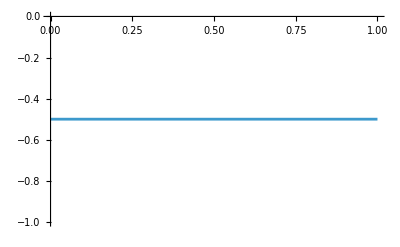

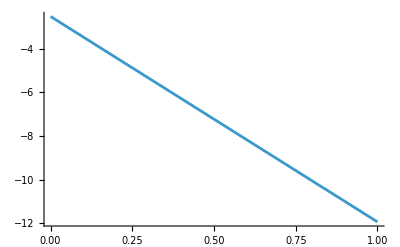

-Graphics-

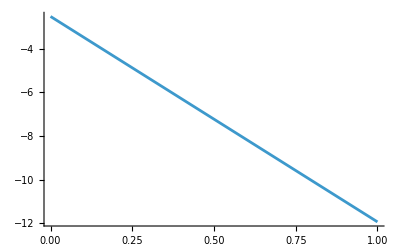

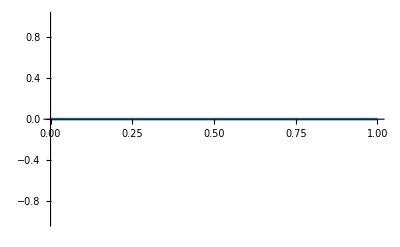

-Graphics-

-Graphics-

-Graphics-

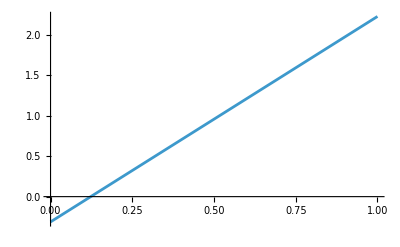

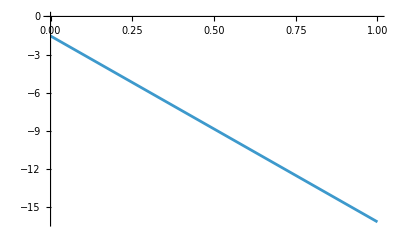

-Graphics-

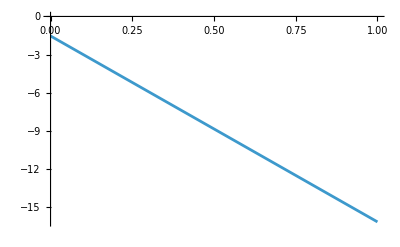

```mathematica
(* Appendix *)

(* We plot the results obtained. These plots should not be taken too seriously, since we only have expansions up to linear order in α *)

lVal = 2;
plotnu0 = Normal[finalnu02] /. l -> lVal;
plotRHS0 = Normal[Series[RHS0Ins /. l -> lVal, {α, 0, 1}]];
Plot[Re[plotnu0 /. l->2], {α,0, 1}]
Plot[Im[plotnu0 /. l-> 2],{α,0,1}]

Plot[Re[plotRHS0 /. l -> 2],{α,0,1}]
Plot[Im[plotRHS0 /. l->2],{α,0, 1}]

plotnu1 = Normal[finalnu11] /. l -> lVal;
plotRHS1 = Normal[Series[RHS1Ins /. l -> lVal, {α, 0, 1}]];
Plot[Re[plotnu1 /. l->2], {α,0, 1}]
Plot[Im[plotnu1 /. l-> 2],{α,0,1}]

Plot[Re[plotRHS1 /. l -> 2],{α,0,1}]
Plot[Im[plotRHS1 /. l->2],{α,0, 1}]

plotnu2 = Normal[finalnu22QNM] /. l -> lVal;
plotRHS2 = Normal[Series[RHS2Ins /. l -> lVal, {α, 0, 1}]];
Plot[Re[plotnu2 /. l->2], {α,0, 1}]
Plot[Im[plotnu2 /. l-> 2],{α,0,1}]

Plot[Re[plotRHS2 /. l -> 2],{α,0,1}]
Plot[Im[plotRHS2 /. l->2],{α,0, 1}]
```